```mathematica
boltzConstEv=8.61733034*10^(-5) eV/kelvin;
boltzConstAngst=138.064852 angstrom^3 bar/kelvin;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"extracted-data.wl"
allTypes=Import["allTypes.dat","List"];
allIsotherms=Import["isothermOutput/all-isotherms.dat","List"];
```

```mathematica
refGibbsEnergy=Association[];
refGibbsEnergy75=Association[];
refGibbsEnergy125=Association[];
refGibbsEnergy175=Association[];
gibbsEnergyPhaseFit=Association[];
isothermInterpolation=Association[];
isothermFit=Association[];
isothermVolFit=Association[];
isothermDensPress=Association[];
isothermVolMinMax=Association[];
isothermRhoMinMax=Association[];
isobarInterpolation=Association[];
isobarTempMinMax=Association[];
```

```mathematica
For[tt=1,tt<=Length[allTypes],tt++,
 currType=allTypes[[tt]];
AssociateTo[refGibbsEnergy,currType -> refMu25[currType]/(25 kelvin*boltzConstEv)];
If[refMu75[currType]/eV < 0,
AssociateTo[refGibbsEnergy75,currType -> refMu75[currType]/(75 kelvin*boltzConstEv)];
];
If[refMu125[currType]/eV < 0,
AssociateTo[refGibbsEnergy125,currType -> refMu125[currType]/(125 kelvin*boltzConstEv)];
];
If[refMu175[currType]/eV < 0,
AssociateTo[refGibbsEnergy175,currType -> refMu175[currType]/(175 kelvin*boltzConstEv)];
]
]
```

```mathematica
isobarInterpolation=Association[];
isobarTempMinMax=Association[];
gibbsEnergyIsobar[type_,TTT_?NumericQ]:=If[isobarTempMinMax[type][[1]][[1]] <= TTT <= isobarTempMinMax[type][[1]][[2]],
refGibbsEnergy[type] -  NIntegrate[isobarInterpolation[type],{x,25,TTT}],Indeterminate]
gibbsEnergyIsobar75[type_,TTT_?NumericQ]:=If[isobarTempMinMax[type][[1]][[1]] <= TTT <= isobarTempMinMax[type][[1]][[2]],
refGibbsEnergy75[type] -  NIntegrate[isobarInterpolation[type],{x,75,TTT}],Indeterminate]
gibbsEnergyIsobar125[type_,TTT_?NumericQ]:=If[isobarTempMinMax[type][[1]][[1]] <= TTT <= isobarTempMinMax[type][[1]][[2]],
refGibbsEnergy125[type] -  NIntegrate[isobarInterpolation[type],{x,125,TTT}],Indeterminate]
gibbsEnergyIsobar175[type_,TTT_?NumericQ]:=If[isobarTempMinMax[type][[1]][[1]] <= TTT <= isobarTempMinMax[type][[1]][[2]],
refGibbsEnergy175[type] -  NIntegrate[isobarInterpolation[type],{x,175,TTT}],Indeterminate]

gibbsEnergyIsobarComb[type_,TTT_?NumericQ]:=If[isobarTempMinMax[type][[1]][[1]] <= TTT <= isobarTempMinMax[type][[1]][[2]],
If[type=="liquid", (*  use coexistence point determined by direct coexistence *)
gibbsEnergyPhaseIsotherm["iceIh",279.5,0]-  NIntegrate[isobarInterpolation[type],{x,279.5,TTT}]
,
If[NumericQ[refGibbsEnergy175[type]],refGibbsEnergy175[type] -  NIntegrate[isobarInterpolation[type],{x,175,TTT}],
If[NumericQ[refGibbsEnergy125[type]],refGibbsEnergy125[type] -  NIntegrate[isobarInterpolation[type],{x,125,TTT}],
If[NumericQ[refGibbsEnergy75[type]],refGibbsEnergy75[type] -  NIntegrate[isobarInterpolation[type],{x,75,TTT}],
refGibbsEnergy[type] -  NIntegrate[isobarInterpolation[type],{x,25,TTT}]]],Indeterminate]]]

For[tt=1,tt<=Length[allTypes],tt++,
currType=allTypes[[tt]];
data = "isobarOutput/isobarOutput-"<>currType<>"-combined.dat";
Print["loading isobaroutput: ", data];
isobarData=Import[data,"Table"];
(*  the integrand is scaled with the number of atoms, rather than the number of molecules, hence the multiplication by 3. H = etotal + PV, and this includes kinetic energy. I.e. we are using the *full* expression for the de Broglie thermal wavelength. *)
Clear[integrand];
integrand={}; 
For[ii=2,ii<=Length[isobarData],ii++,
integrand=Join[integrand,{{isobarData[[ii]][[2]], 3*(isobarData[[ii]][[5]]+isobarData[[ii]][[6]]/isobarData[[ii]][[4]]*6.24150913*10^-7)/(boltzConstEv * isobarData[[ii]][[2]]^2)+ 9/2/isobarData[[ii]][[2]]  /.eV->1/.kelvin->1 }}]];
(*integrand=Join[integrand,{{isobarData[[ii]][[2]], 3*(isobarData[[ii]][[5]]+isobarData[[ii]][[6]]/isobarData[[ii]][[4]]*6.24150913*10^-7)/(boltzConstEv)+ 9/2  * isobarData[[ii]][[2]]  /.eV->1/.kelvin->1 }}]];*)
tempDensity={}; For[ii=2,ii<=Length[isobarData],ii++,tempDensity=Join[tempDensity,{{isobarData[[ii]][[1]], isobarData[[ii]][[4]]}}]];
integrand=DeleteDuplicatesBy[integrand,First];
integrandTempInt=Interpolation[integrand,InterpolationOrder->1, "ExtrapolationHandler" -> {Indeterminate &, "WarningMessage" -> False}];
model=a + (b+c x+d x^2+ e x^3 )/x^2;
nlm=NonlinearModelFit[integrand,{model},{{a,0},{b,-100000},{c,2},{d,1},e},x];
fitIsobar=Normal[nlm];
AssociateTo[isobarTempMinMax, currType->integrandTempInt["Domain"]];
AssociateTo[isobarInterpolation, currType -> fitIsobar];
(*Show[ListPlot[integrand,PlotRange->{{25,50},All}],Plot[{integrandTempInt[x],fitIsobar,isobarInterpolation["iceIII"]},{x,25,50}]]//Print;*)
 (*Show[ListPlot[tempDensity],PlotRange->{{20,50},Automatic}]//Print;*)
]
```

loading isobaroutput: isobarOutput/isobarOutput-ice12111-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceXI-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceII-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceIX-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceXIII-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceXIV-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceXV-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceLTA-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceMAR-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceNON-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-icei-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice0-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceACO-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceBSV-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceDOH-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice11215848-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice12232449-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice14427301-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice15124949650-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice1532155471-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice16927915-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice17625256-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice20228176-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice533726600-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice582511-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice6128842-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice6721563-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-ice8421419-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-icePCOD8007225-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-icePCOD8036144-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-icePCOD8047078-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-icePCOD8047931-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-icePCOD8204698-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-icePCOD8301974-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-icePCOD8321499-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-icePCOD8324623-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceIc-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceIh-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceIII-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceIV-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceV-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-liquid-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceVIII-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceVII-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceVI-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceIII-part-combined.dat

loading isobaroutput: isobarOutput/isobarOutput-iceV-part-combined.dat

```mathematica
(*  proton disorder added here as a constant: 'gibbsEnergyPhaseIsotherm' is actually divided by k_B*T. We assume the proton disorder entropy, taken from 10.1063/1.4882650, doesn't itself change with temperature. *)
(* ices III and V are partially proton-ordered - we use the values from 10.1063/1.1808693 instead  *)
```

```mathematica
protonDisorder=Association[];  (* first suppose there is no proton disorder, then add explicit values for the known phases *)
For[tt = 1, tt <= Length[allTypes], tt++,
  currType = allTypes[[tt]];
  AssociateTo[protonDisorder, currType->0];
  ]
 AssociateTo[protonDisorder,"iceIh"->0.41069];  (*  the proton ordered form is ice XI *)
 AssociateTo[protonDisorder,"iceIc"-> 0.41064]; (*  the proton ordered form is ice XIc, which is called ice12111 here *)
 AssociateTo[protonDisorder,"iceVII"-> 0.41064]; (*  ice VII is equivalent to ice Ic, with two interpenetrating networks *)
 (*AssociateTo[protonDisorder,"iceIII"->0.41165];(*  the proton ordered form is ice IX *)*)
AssociateTo[protonDisorder,"iceIII"->0.3686];(*  the proton ordered form is ice IX *)
AssociateTo[protonDisorder,"iceIII-part"->0.3686];(*  the proton ordered form is ice IX *)
 AssociateTo[protonDisorder,"iceIV"->0.40847];(*  the proton ordered form is not known *)
(*AssociateTo[protonDisorder,"iceV"->0.41316]; (*  the proton ordered form is ice XIII *)*)
AssociateTo[protonDisorder,"iceV"->0.3817];(*  the proton ordered form is ice IX *)
AssociateTo[protonDisorder,"iceV-part"->0.3817];(*  the proton ordered form is ice IX *)
 AssociateTo[protonDisorder,"iceVI"->0.42138]; (*  the proton ordered form is ice XV *)
 AssociateTo[protonDisorder,"iceVI-small"->0.42138]; (*  the proton ordered form is ice XV *)
 AssociateTo[protonDisorder,"iceXII"->0.40813]; (*  the proton ordered form is ice XIV *)
```

```mathematica
gibbsEnergyPhaseIsotherm[type_,TTT_?NumericQ,PPP_?NumericQ]:=If[KeyExistsQ[isothermVolMinMax,type[TTT]] && (isothermVolMinMax[type[TTT]][[1]][[1]]< PPP < isothermVolMinMax[type[TTT]][[1]][[2]]),
gibbsEnergyIsobarComb[type, TTT] + NIntegrate[isothermInterpolation[type[TTT]],{x,0,PPP}] -  protonDisorder[type]  ,Indeterminate]
```

```mathematica
For[kk=1,kk<=Length[allIsotherms], kk++,
currEntry=ToExpression[allIsotherms[[kk]]];
data=StringJoin["isothermOutput/isotherm-T",ToString[currEntry[[1]]],"-",currEntry[[2]],".dat"];
(*Print["will load: ", data];*)
currType=currEntry[[2]];
currTemp=currEntry[[1]];
If[isobarTempMinMax[currType][[1]][[1]] <= currTemp <= isobarTempMinMax[currType][[1]][[2]],
isothermData=Import[data,"Table"];
(* column 7 is the volume per particle, but we want the volume per formula unit, hence multiply by 3 *)
Clear[integrand]; integrand={};
For[ii=2,ii<=Length[isothermData],ii++,
AppendTo[integrand,{isothermData[[ii]][[3]],3*isothermData[[ii]][[7]]/(boltzConstAngst*isothermData[[ii]][[6]]/.kelvin->1/.bar->1/.angstrom->1)}]];
model=a + b x + c x^2 + d x^3;
If[Length[integrand]<4,model=a + b x + c x^2];
If[Length[integrand]<3,model=a + b x];
integrandVolumeInt=Interpolation[integrand,InterpolationOrder->1, "ExtrapolationHandler" -> {Indeterminate &, "WarningMessage" -> False}];
AssociateTo[isothermVolMinMax, currType[currTemp]->integrandVolumeInt["Domain"]];
AssociateTo[isothermFit, currType[currTemp] -> Normal[NonlinearModelFit[integrand,{model},{a,b,c,d},x]]];
AssociateTo[isothermInterpolation, currType[currTemp] -> Interpolation[integrand,InterpolationOrder->1][x]];
(*Show[Plot[{isothermInterpolation[currType[currTemp]],isothermFit[currType[currTemp]]},{x,0,isothermVolMinMax[currType[currTemp]][[1]][[2]]},PlotStyle->{Green,Blue}],ListPlot[integrand,PlotStyle->{Red}]]//Print;*)
(*Show[Plot[ NIntegrate[isothermInterpolation[currType[currTemp]],{x,0,PPP}],{PPP,0,isothermVolMinMax[currType[currTemp]][[1]][[2]]}]]//Print;*)
]
]
```

Part::partd: Part specification "KeyAbsent" ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification "KeyAbsent" ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification "KeyAbsent" ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

General::stop: Further output of Interpolation :: inhr will be suppressed during this calculation.

```mathematica
importantPhases={"iceIc","iceIh","iceII","iceIX","iceVI","iceXIII","iceXV","liquid","iceV-part","iceIII-part"};
```

Prepare a fit to the ML chemical potential; this helps us to calculate (approximate) coexistence points.

```mathematica
tempList={125,150,175,200,225,250,262.5,275,300,325,350,375};
limitedTypes=allTypes;
fitGibbs=Association[];
Clear[PPP];
For[kk=1,kk<=Length[tempList],kk++,
currTemp=tempList[[kk]];
For[tt=1,tt<=Length[limitedTypes],tt++,
Clear[currTable];currTable={};
currType=limitedTypes[[tt]];
For[ttP=0,ttP<=20000,ttP+=50,
myGibbs=gibbsEnergyPhaseIsotherm[currType,currTemp,ttP];
If[myGibbs<5000000, AppendTo[currTable,{ttP,myGibbs}]];];
If[Length[currTable]>0,
If[currType≠"liquid",
AssociateTo[fitGibbs,currType[currTemp]->Normal[NonlinearModelFit[currTable,{a ppp^3 + b ppp^2 + c ppp + d + e ppp^4},{a,b,c,d,e},ppp]]],
AssociateTo[fitGibbs,currType[currTemp]->Normal[NonlinearModelFit[currTable,{ a Sqrt[ppp] + c ppp + d },{a,b,c,d,e},ppp]]]
]];
]]
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmvali will be suppressed during this calculation.

```mathematica
tempList={125,150,175,200,225,250,262.5,275,300,325,350};
ppp=.;
For[kk=1,kk<=Length[tempList],kk++,
currTemp=tempList[[kk]];
exportList={ppp};
For[tt=1,tt<=Length[allTypes],tt++,
currType=allTypes[[tt]];
If[KeyExistsQ[fitGibbs,currType[currTemp]],
exportList=Join[exportList, {   (fitGibbs[currType[currTemp]]-fitGibbs["iceII"[currTemp]])  * currTemp kelvin * boltzConstEv * 1000/eV  }],
exportList=Join[exportList, {   Indeterminate  }]
]
]

Export["chemical-potential-output/chemPotFitted-"<>ToString[currTemp]<>"K.dat",Join[{Join[{"P/bar"},allTypes]},
Table[exportList/.Indeterminate->NaN,{ppp,0,10000,50}]],"Table"]
]
```

Now deal with NQE corrections and ML -> DFT corrections.

```mathematica
(* use precomputed PIMD corrections, consistently relative to ice II *)
```

```mathematica
nnToDftCorrectionDiscrete=Association[];
pimdCorrectionDiscrete=Association[];
nnToDftTypes=importantPhases;

Clear[data];
For[kk=1,kk<=Length[nnToDftTypes], kk++,
currEntry=nnToDftTypes[[kk]];
AssociateTo[pimdCorrectionDiscrete,currEntry->{}];
data="ice-nnp2dft-results/"<>currEntry<>"-deltamu.dat";
AssociateTo[nnToDftCorrectionDiscrete,currEntry->Import[data,"Table"][[2;;]]];
(* now pimd *)
data="ice-pimd-results/split-up-by-y/split-up-by-PT/"<>currEntry<>"-PIMD-correction.dat";
If[FileExistsQ[data],
importedData=Import[data,"Table"];
(* column 1 = temp, 2 = pressure, 3 = PIMD correction in meV/molecule, 4 = the same, but computed with Simpson's rule )*)
For[ii=1,ii<=Length[importedData],ii++,
AppendTo[pimdCorrectionDiscrete[currEntry],{importedData[[ii]][[1]],importedData[[ii]][[2]],importedData[[ii]][[4]]}];
];
]]

nnToDftCorrectionDiscreteSelector[currType_,myT_,myP_]:= (calcVal=Select[nnToDftCorrectionDiscrete[currType],#1[[1]]==myT && #1[[2]]==myP &][[1]][[3]] ; If[NumericQ[calcVal],calcVal,Indeterminate])
pimdCorrectionDiscreteSelector[currType_,myT_,myP_]:= (calcVal=Select[pimdCorrectionDiscrete[currType],#1[[1]]==myT && #1[[2]]==myP &][[1]][[3]] ; If[NumericQ[calcVal],calcVal,Indeterminate])
```

```mathematica
pimdCorrectionExtrapolation=Association[];

For[kk=1,kk<=Length[nnToDftTypes], kk++,
currEntry=nnToDftTypes[[kk]];
For[myPP=0,myPP<=10000,myPP+=1000,
If[currEntry != "liquid",
currTable=Select[pimdCorrectionDiscrete[currEntry],#1[[2]]==myPP && 125<= #1[[1]] <= 250  && #1[[1]] != 175 &][[All,{1,3}]],
currTable=Select[pimdCorrectionDiscrete[currEntry],#1[[2]]==myPP && 225<= #1[[1]] <= 325 &][[All,{1,3}]];
];
fitted=Normal[NonlinearModelFit[currTable,{a + b temperature},{a,b},temperature]];
AssociateTo[pimdCorrectionExtrapolation,currEntry[myPP]->fitted];
(*Show[ListPlot[currTable], Plot[fitted,{temperature,0,300}], PlotLabel->currEntry.myPP]//Print;*)
]]

extrapolatedPimdCorrectionDiscreteSelector[currType_,myT_,myP_]:= (If[KeyExistsQ[pimdCorrectionExtrapolation,currType[myP]], pimdCorrectionExtrapolation[currType[myP]]/.temperature->myT, Indeterminate])
```

```mathematica
overallChemPot[currType_,currTemp_,myP_]:=
If[KeyExistsQ[fitGibbs,currType[currTemp]],
If[(currType=="liquid")&&myP>4500,Indeterminate,
fitGibbs[currType[currTemp]]*currTemp*boltzConstEv  + nnToDftCorrectionDiscreteSelector[currType,currTemp,myP] + pimdCorrectionDiscreteSelector[currType,currTemp,myP]/.eV->1000/.kelvin->1 /.ppp->myP],
Indeterminate]
```

```mathematica
tempList={125,150,175,200,225,250,275,300};
For[kk=1,kk<=Length[tempList],kk++,
exportList={};
currTemp=tempList[[kk]];
For[PPP=0, PPP<=10000, PPP+=1000,
exportInner={PPP};
For[tt=1,tt<=Length[nnToDftTypes],tt++,
currType=nnToDftTypes[[tt]];
exportInner=Join[exportInner, {   overallChemPot[currType,currTemp, PPP] - overallChemPot["iceII",currTemp, PPP] }]
];
exportList=Join[exportList,{exportInner}];
];
Export["chemical-potential-output/chemPotFullNoFit-"<>ToString[currTemp]<>"K.dat",Join[{Join[{"P/bar"},nnToDftTypes]},
exportList/.Indeterminate->NaN],"Table"]
]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {} ⟦ 1 ⟧ does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
tempList={125,150,175,200,225,250,275,300};
limitedTypes=nnToDftTypes;
fitGibbsFull=Association[];
Clear[PPP];
For[kk=1,kk<=Length[tempList],kk++,
currTemp=tempList[[kk]];
For[tt=1,tt<=Length[limitedTypes],tt++,
Clear[currTable];currTable={};
currType=limitedTypes[[tt]];
For[ttP=0,ttP<=10000,ttP+=1000,
myGibbs=overallChemPot[currType,currTemp,ttP];
If[currType=="liquid" && ttP>4500, myGibbs=15000000];
If[myGibbs<5000000, AppendTo[currTable,{ttP,myGibbs}]];];
If[Length[currTable]>0,AssociateTo[fitGibbsFull,currType[currTemp]->Normal[NonlinearModelFit[currTable,{c ppp + d},{c,d},ppp]]];
(*Show[ListPlot[currTable],Plot[fitGibbsFull[currType[currTemp]],{ppp,0,10000}],PlotLabel->currType.currTemp]//Print*)];
];
]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {} ⟦ 1 ⟧ does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
tempList={125,150,175,200,225,250,275,300};
For[kk=1,kk<=Length[tempList],kk++,
exportList={};
currTemp=tempList[[kk]];
For[PPP=0, PPP<=10000, PPP+=1000,
exportInner={PPP};
For[tt=1,tt<=Length[nnToDftTypes],tt++,
currType=nnToDftTypes[[tt]];
If[KeyExistsQ[fitGibbsFull,currType[currTemp]], myVal=fitGibbsFull[currType[currTemp]] - fitGibbsFull["iceII"[currTemp]]/.ppp-> PPP , myVal=Indeterminate];
exportInner=Join[exportInner, {   myVal }]
];
exportList=Join[exportList,{exportInner}];
];
Export["chemical-potential-output/chemPotFullFitted-"<>ToString[currTemp]<>"K.dat",Join[{Join[{"P/bar"},nnToDftTypes]},
exportList/.Indeterminate->NaN],"Table"]
]
```

Example chemical potential plot.

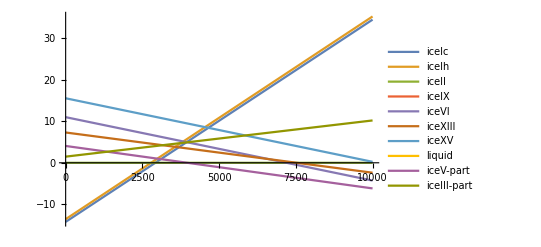

```mathematica
myLists=nnToDftTypes;
currTemp=225;
plotComb={};
For[tt=1,tt<=Length[myLists],tt++,
currType=myLists[[tt]];
plotComb=Join[plotComb, {fitGibbsFull[currType[currTemp]] - fitGibbsFull["iceII"[currTemp]]}]
]
Plot[plotComb,{ppp,0,10000},PlotLegends->myLists]
```

```mathematica
findCoexFull[phaseA_,phaseB_,currTemp_,currGuess_:3000]:={currTemp,ppp/.FindRoot[Abs[fitGibbsFull[phaseA[currTemp]]-fitGibbsFull[phaseB[currTemp]]]==0,{ppp,currGuess},MaxIterations->200000][[1]]}
```

Find coexistence points for all pairs of phases. Some obviously have no crossovers, so the following will spit out a few warnings, but that’s OK.

```mathematica
Clear[phaseCoexLimits];
phaseCoexLimits=Association[];
AssociateTo[phaseCoexLimits,Sort[{"iceII","iceVI"}]->{100,225}];
AssociateTo[phaseCoexLimits,Sort[{"iceII","iceV-part"}]->{150,250}];
AssociateTo[phaseCoexLimits,Sort[{"iceIc","iceV-part"}]->{100,275}];
AssociateTo[phaseCoexLimits,Sort[{"iceII","iceIc"}]->{150,250}];

limitedTypes=nnToDftTypes;
Clear[coexCurves,coexCurvesPts];
coexCurves=Association[];
coexCurvesPts=Association[];
For[ph1id=1,ph1id<Length[limitedTypes],ph1id++,
phase1=limitedTypes[[ph1id]];
For[ph2id=ph1id+1,ph2id<=Length[limitedTypes],ph2id++,
phase2=limitedTypes[[ph2id]];
Clear[currList]; currList={};
myMin=If[(NumericQ[phaseCoexLimits[Sort[{phase1,phase2}]][[1]]]) && (phaseCoexLimits[Sort[{phase1,phase2}]][[1]] > -100), phaseCoexLimits[Sort[{phase1,phase2}]][[1]], 25];
myMax=If[(NumericQ[phaseCoexLimits[Sort[{phase1,phase2}]][[1]]]) && (phaseCoexLimits[Sort[{phase1,phase2}]][[1]] > -100), phaseCoexLimits[Sort[{phase1,phase2}]][[2]], 300];
For[ii=myMin,ii<=myMax,ii+=25,
initGuess=(isothermVolMinMax[phase1[ii]][[1]][[1]] + isothermVolMinMax[phase2[ii]][[1]][[1]] + isothermVolMinMax[phase1[ii]][[1]][[2]] + isothermVolMinMax[phase2[ii]][[1]][[2]])/4;
initGuess=Min[initGuess,0.9*isothermVolMinMax[phase1[ii]][[1]][[2]],0.9*isothermVolMinMax[phase2[ii]][[1]][[2]] ];
coexPt=findCoexFull[phase1, phase2, ii,initGuess];
If[coexPt[[2]] != initGuess, 
AppendTo[currList, coexPt]];
(*Print["here : ", ii, " - ", initGuess, " - ", coexPt, " - ", phase1, "  ", phase2, " list: ", currList];*)
];
If[Length[currList]>1,
AssociateTo[coexCurves,{phase1,phase2}->Normal[NonlinearModelFit[currList,{a x^2 + b x + d},{a,b,c,d,e,f,g},x]]];
AssociateTo[coexCurvesPts,{phase1,phase2}->currList];
AssociateTo[coexCurves,{phase2,phase1}->coexCurves[{phase1,phase2}]];
AssociateTo[coexCurvesPts,{phase2,phase1}->coexCurvesPts[{phase1,phase2}]];
]
(*Show[ListPlot[currList,PlotLabel->"coex: "<>phase1<>" and "<>phase2],Plot[coexCurves[{phase1,phase2}],{x,25,350}]]//Print;*)
];]

curveCross=Association[];
For[ii=1,ii<Length[coexCurves],ii++,
setA=Keys[coexCurves][[ii]];
For[kk=ii+1,kk<=Length[coexCurves],kk++,
setB=Keys[coexCurves][[kk]];
If[Not[(setA[[1]]==setB[[2]] && setA[[2]]==setB[[1]])],
currTemp=(x/.FindRoot[coexCurves[setA]==coexCurves[setB],{x,200}]);
currPress=coexCurves[setA]/.x->currTemp;
AssociateTo[curveCross,{setA,setB}->{currTemp,currPress}];
AssociateTo[curveCross,{setB,setA}->{currTemp,currPress}];
];
]]
```

FindRoot::nlnum: The function value {Abs[Missing["KeyAbsent", "iceIc"[25.]] - 1.\ Missing["KeyAbsent", "iceIh"[25.]]]} is not a list of numbers with dimensions {1} at {ppp} = {10100.5}.

ReplaceAll::reps: {Abs[Missing["KeyAbsent", "iceIc"[25]] - Missing["KeyAbsent", "iceIh"[25]]] == 0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification "KeyAbsent" ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification "KeyAbsent" ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

FindRoot::srect: Value Min[0.9\ "KeyAbsent" ⟦ 2 ⟧, 1/4\ (2\ "KeyAbsent" ⟦ 1 ⟧ + 2\ "KeyAbsent" ⟦ 2 ⟧)] in search specification {ppp, Min[0.9\ "KeyAbsent" ⟦ 2 ⟧, 1/4\ (2\ "KeyAbsent" ⟦ 1 ⟧ + 2\ "KeyAbsent" ⟦ 2 ⟧)]} is not a number or array of numbers.

ReplaceAll::reps: {Abs[Missing["KeyAbsent", "iceIc"[50]] - Missing["KeyAbsent", "iceIh"[50]]] == 0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {Abs[Missing["KeyAbsent", "iceIc"[75.]] - 1.\ Missing["KeyAbsent", "iceIh"[75.]]]} is not a list of numbers with dimensions {1} at {ppp} = {9475.41}.

FindRoot::srect: Value Min[0.9\ "KeyAbsent" ⟦ 2 ⟧, 1/4\ (2\ "KeyAbsent" ⟦ 1 ⟧ + 2\ "KeyAbsent" ⟦ 2 ⟧)] in search specification {ppp, Min[0.9\ "KeyAbsent" ⟦ 2 ⟧, 1/4\ (2\ "KeyAbsent" ⟦ 1 ⟧ + 2\ "KeyAbsent" ⟦ 2 ⟧)]} is not a number or array of numbers.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

FindRoot::nlnum: The function value {Abs[Missing["KeyAbsent", "iceIc"[25.]] - 1.\ Missing["KeyAbsent", "iceIX"[25.]]]} is not a list of numbers with dimensions {1} at {ppp} = {9718.88}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

FindRoot::srect: Value Min[0.9\ "KeyAbsent" ⟦ 2 ⟧, 1/4\ (2\ "KeyAbsent" ⟦ 1 ⟧ + 2\ "KeyAbsent" ⟦ 2 ⟧)] in search specification {ppp, Min[0.9\ "KeyAbsent" ⟦ 2 ⟧, 1/4\ (2\ "KeyAbsent" ⟦ 1 ⟧ + 2\ "KeyAbsent" ⟦ 2 ⟧)]} is not a number or array of numbers.

General::stop: Further output of FindRoot :: srect will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

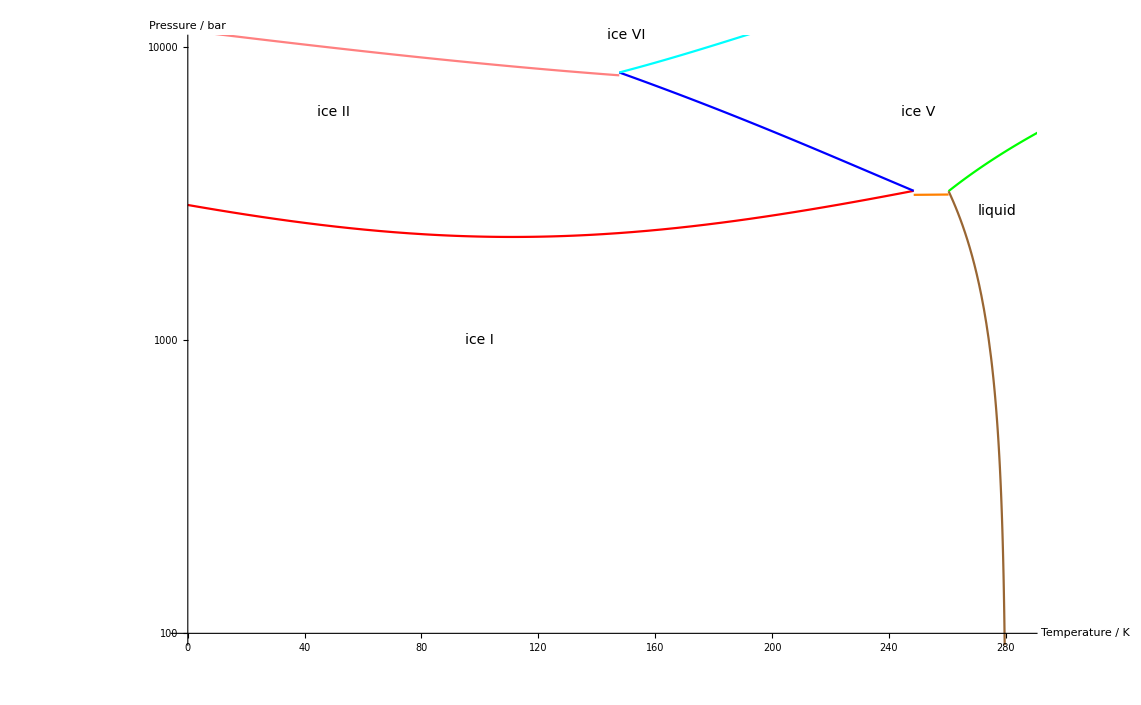

```mathematica
plotIvsII=LogPlot[coexCurves[{"iceIc","iceII"}],{x,0,curveCross[{{"iceII","iceIc"},{"iceII","iceV-part"}}][[1]]},PlotStyle->Red];
plotVvsII=LogPlot[coexCurves[{"iceII","iceV-part"}],{x,curveCross[{{"iceII","iceV-part"},{"iceV-part","iceVI"}}][[1]],curveCross[{{"iceII","iceIc"},{"iceII","iceV-part"}}][[1]]},PlotStyle->Blue];
plotVvsLiq=LogPlot[coexCurves[{"liquid","iceV-part"}],{x,curveCross[{{"liquid","iceIc"},{"liquid","iceV-part"}}][[1]],300},PlotStyle->Green];
plotIvsLiq=LogPlot[coexCurves[{"liquid","iceIc"}],{x,curveCross[{{"liquid","iceIc"},{"liquid","iceV-part"}}][[1]],300},PlotStyle->Brown];
plotVvsVI=LogPlot[coexCurves[{"iceV-part","iceVI"}],{x,curveCross[{{"iceII","iceV-part"},{"iceV-part","iceVI"}}][[1]],300},PlotStyle->Cyan];
plotIIvsVI=LogPlot[coexCurves[{"iceII","iceVI"}],{x,0,curveCross[{{"iceII","iceV-part"},{"iceV-part","iceVI"}}][[1]]},PlotStyle->Pink];
plotIvsV=LogPlot[coexCurves[{"iceV-part","iceIc"}],{x,curveCross[{{"iceII","iceIc"},{"iceII","iceV-part"}}][[1]],curveCross[{{"liquid","iceIc"},{"liquid","iceV-part"}}][[1]]},PlotStyle->Orange];

Show[plotIvsII,plotVvsII,plotVvsLiq,plotIvsLiq,plotIvsV,plotVvsVI,plotIIvsVI,PlotRange->{{0,285},{Log[100],Log[10000]}},AxesOrigin->{0,Log[100]},
  Epilog -> {Text[Style["ice I", 14], {100, Log[1000]}],Text[Style["ice II", 14], {50,Log[6000]}],Text[Style["ice V", 14], {250,Log[6000]}],Text[Style["ice VI", 14], {150,Log[11000]}],Text[Style["liquid", 14], {277,Log[2750]}]},AxesLabel->{"Temperature / K","Pressure / bar"}] (*,PointSize[Medium],Point[coexCurvesPts[{"ice12111","iceIc"}]]}]*)
```